```mathematica
Manipulate[
p = Exp[alpha + beta*Log[PreyMass/PredMass] + gamma*Log[PreyMass/PredMass]^2];
prob = p/(1+p);
Plot[prob,{PreyMass,0,1000},PlotRange->{0,1}],
{{PredMass,50},1,1000},
{{alpha,-1.77},-4,4},
{{beta,-8.54},-10,4},
{{gamma,-3.33},-4,4}]
```

```mathematica
α = -0.92
β = -8.54
γ = -3.5
```

-0.92

-8.54

-3.5

```mathematica
bodysize = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/bodysizedata.csv","Data"];
fmatrix = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/foraging_matrix.csv","Data"];
OccHist =  Delete[bodysize[[All,4]],1];
OccCurr =  Delete[bodysize[[All,5]],1];
```

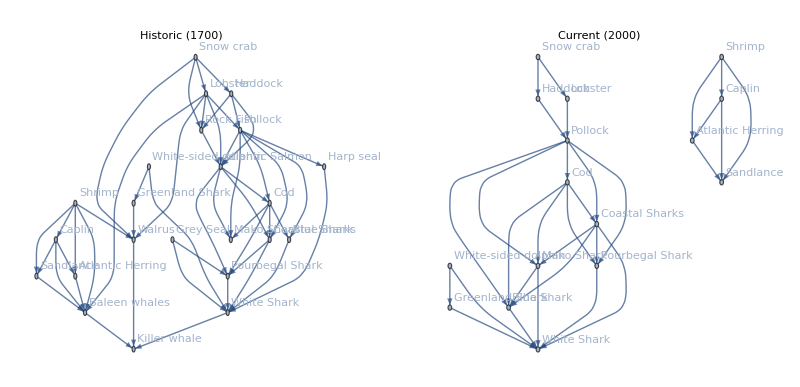

```mathematica
NetOut =Table[0,{l,1,2}];
Labels = {"Historic (1700)","Current (2000)"};
For[k=1,k<3,k++,
Occ = Delete[bodysize[[All,3+k]],1];
Extinct =Position[Occ,0];
fwsize = Length[Position[Occ,1]];
BMmin = Delete[bodysize[[All,2]],1]; BMmin = Delete[BMmin,Extinct];
BMmax = Delete[bodysize[[All,3]],1]; BMmax = Delete[BMmax,Extinct];
BMavg = N[Mean[{BMmin,BMmax}]];
Spp = Delete[fmatrix[[1,All]],1];(*This gets rid of the label*) Spp = Delete[Spp,Extinct];(*This gets rid of the extinct species*)
f = fmatrix[[2;;Length[fmatrix],2;;Length[fmatrix]]];
f = Delete[f,Extinct];
f = Transpose[Delete[Transpose[f],Extinct]];
PRint = Table[
p = Exp[α + β*Log[BMavg[[j]]/BMavg[[i]]] + γ*Log[BMavg[[j]]/BMavg[[i]]]^2 + f[[i,j]]];
p/(1+p),
{i,1,fwsize},
{j,1,fwsize}
];
fw = Table[
If[i<j,
rv = RandomReal[];
If[
rv < PRint[[i,j]],
1,0],
0],
{i,1,fwsize},
{j,1,fwsize}
];
NetOut[[k]]=AdjacencyGraph[
Transpose[fw],VertexLabels->Table[i->Spp[[i]],{i,1,fwsize}],PlotLabel->Labels[[k]]]
]
GG =GraphicsGrid[{NetOut},ImageSize->800]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/FigureNet.PDF",GG]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/FigureNet.PDF

```mathematica
NetOut =Table[0,{i,1,2}]
```

{0,0}

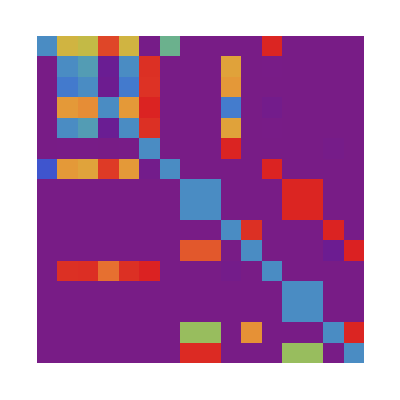

```mathematica
ArrayPlot[PRint,ColorFunction->"Rainbow"]
```

```mathematica
f
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}